```mathematica
Clear[Lx,Ly,A,B,
sx2d,SX2D,
sy2d,SY2D,sy2dp,SY2DP,
cx2d,CX2D,
cy2d,CY2D,cy2dp,CY2DP,
cons,Cons]
```

```mathematica
Lx=32;
Ly=32;
midPtX = Floor[Lx/2];
midPtY = Floor[Ly/2];
A=Lx*Ly;
Lz=20;
```

```mathematica
B=0.1*2*π;
```

```mathematica
(** In our units, phi0 = 2 * pi * hbar/e = 2 pi **)
```

```mathematica
(** Also, B = phi, because area of plaquet is 1 square unit. Hence, we are taking B in the units of 2 pi, so that phi/phi0 will be a nice decimal fraction like 0.02**)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sx2d[i_Integer,j_Integer]=0;

Do[Do[{sx2d[j+k Lx,j+1+k Lx]=-I/2,sx2d[j+1+k Lx,j+k Lx]=I/2},{j,1,Lx-1}],{k,0,Ly-1}]

SX2D=Table[sx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sy2d[i_Integer,j_Integer]=0;

Do[Do[{sy2d[k Lx+j,(k+1)Lx+j]=-I/2,sy2d[(k+1)Lx+j,k Lx+j]=I/2},{j,1,Lx}],{k,0,Ly-2}]
Do[Do[{sy2d[k Lx+j,(k+1)Lx+j]=-I/2 Exp[- I B],sy2d[(k+1)Lx+j,k Lx+j]=I/2 Exp[ I B]},{j,midPtX+1,Lx}],{k,midPtY,midPtY}]

SY2D=Table[sy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sy2dp[i_Integer,j_Integer]=0;

Do[{sy2dp[(Ly-1)Lx+j,j]=-I/2,sy2dp[j,(Ly-1)Lx+j]=I/2},{j,1,Lx}]

SY2DP=Table[sy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cx2d[i_Integer,j_Integer]=0;

Do[Do[{cx2d[j+k Lx,j+1+k Lx]=1/2,cx2d[j+1+k Lx,j+k Lx]=1/2},{j,1,Lx-1}],{k,0,Ly-1}]

CX2D=Table[cx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cy2d[i_Integer,j_Integer]=0;

Do[Do[{cy2d[k Lx+j,(k+1)Lx+j]=1/2,cy2d[(k+1)Lx+j,k Lx+j]=1/2},{j,1,Lx}],{k,0,Ly-2}]
Do[Do[{cy2d[k Lx+j,(k+1)Lx+j]=1/2 Exp[- I B],cy2d[(k+1)Lx+j,k Lx+j]=1/2 Exp[I B]},{j,midPtX+1,Lx}],{k,midPtY,midPtY}]

CY2D=Table[cy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cy2dp[i_Integer,j_Integer]=0;

Do[{cy2dp[(Ly-1)Lx+j,j]=1/2,cy2dp[j,(Ly-1)Lx+j]=1/2},{j,1,Lx}]

CY2DP=Table[cy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------- Lattice model for a constant matrix ---------------*)
```

```mathematica
cons[i_Integer, j_Integer]:=0

Do[{cons[i,i]=1},{i,1,A}]

Cons=Table[cons[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[σ0,σ1,σ2,σ3,HamiltonianWSM1, HamiltonianWSM2]
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
(* HamiltonianQAHI[t_,t0_,m_,α_]:=t*(KroneckerProduct[SX2D+α*SX2DP,σ1]+KroneckerProduct[SY2D+α*SY2DP, σ2])+KroneckerProduct[-m*Cons+t0*(CX2D+CY2D+α*CX2DP+α*CY2DP),σ3] *)
```

```mathematica
(* HamiltonianQAHI[t_,t0_,m_,kz_]:=t*(KroneckerProduct[SX2D,σ1]+KroneckerProduct[SY2D, σ2])+KroneckerProduct[-m*Cons+t0*(CX2D+CY2D),σ3] +Cos[kz]*KroneckerProduct[Cons,σ3] *)
```

```mathematica
HamiltonianWSM1[t_,t0_,m_,tz_,kz_, αy_]:=t*(KroneckerProduct[SX2D,σ1]+KroneckerProduct[SY2D+αy*SY2DP, σ2])+KroneckerProduct[2*Cons-t0*(CX2D+CY2D+αy*CY2DP),σ3]+KroneckerProduct[(tz *Cos[kz]-m)*Cons,σ3]
```

```mathematica
HamiltonianWSM2[t_,m_,kz_,αy_,tx_]:=2t*(KroneckerProduct[SX2D,σ1]+KroneckerProduct[SY2D+αy*SY2DP, σ2])+2m * KroneckerProduct[2*Cons-(CX2D+CY2D+αy*CY2DP),σ3]+KroneckerProduct[(2 t *Cos[kz])*Cons,σ3]-2 tx * KroneckerProduct[SX2D,σ0]
```

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[val,vec,ValVecAHI,ValAHI,ValAHIRange,β]
```

```mathematica
β=-1.75;
```

```mathematica
{val,vec}=Eigensystem[HamiltonianWSM1[1.,1.,0,1,(β π)/2,0]];
```

```mathematica
ValVecAHI=SortBy[Transpose[{val,vec}],First];
```

```mathematica
ValAHI=Table[{j,Re[ValVecAHI[[j,1]]]},{j,1,2A}];
```

```mathematica
ValAHIRange=Table[ValAHI[[j,2]],{j,1,2 A}];
```

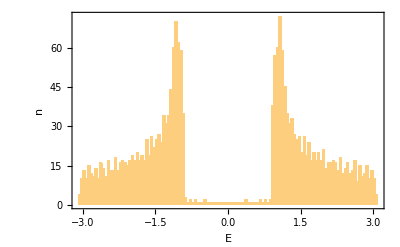

```mathematica
Show[Histogram[val,100],PlotRange-> All, Frame-> True, FrameLabel-> {"E","n"},BaseStyle-> 16,FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}}]
```

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[kzVector]
```

```mathematica
kzVector = N@Subdivide[-π,π,Lz-1]
```

{-3.14159,-2.8109,-2.4802,-2.14951,-1.81882,-1.48812,-1.15743,-0.826735,-0.496041,-0.165347,0.165347,0.496041,0.826735,1.15743,1.48812,1.81882,2.14951,2.4802,2.8109,3.14159}

```mathematica
NumPoints=Dimensions[kzVector][[1]]
```

20

```mathematica
(** Calculate Charge density as a function of position **)
```

```mathematica
Clear[ChargeXY, ChargeXYFlatten, ChargeXYPlot]
```

```mathematica
ChargeXY = Table[{x,y,0},{x,1,Lx},{y,1,Ly}];
```

```mathematica
Dimensions[ChargeXY]
```

{32,32,3}

```mathematica
Do[{Clear[HTrial,ValueFibon,VecFibon,ValFibon,OnlyEigenvalue,ValVecFibon],
HTrial =HamiltonianWSM1[1,1,0,1,kzVector[[kzIndex]],1],
{ValueFibon,VecFibon}=Eigensystem[HTrial],
ValVecFibon=SortBy[Transpose[{ValueFibon,VecFibon}],First],
Do[Do[Do[ChargeXY[[x,y]][[3]] += Abs[ValVecFibon[[J,2,2(x + (y-1)Lx)]]]^2+Abs[ValVecFibon[[J,2,2(x + (y-1)Lx)-1]]]^2,{x,1,Lx}],{y,1,Ly}],{J,1,A}]},{kzIndex ,1,Lz}];
```

```mathematica
ChargeXY;
```

```mathematica
ChargeXYFlatten = Flatten[ChargeXY];
```

```mathematica
Dimensions[ChargeXYFlatten][[1]]
```

3072

```mathematica
Lx*Ly*3
```

3072

```mathematica
ChargeXYFlatten[[18]]
```

19.8694

```mathematica
ChargeXYPlot = Table[{ChargeXYFlatten[[3i-2]],ChargeXYFlatten[[3i-1]],ChargeXYFlatten[[3i]]},{i,1,Dimensions[ChargeXYFlatten][[1]]/3}]
```

{{1,1,19.8694},{1,2,19.8694},{1,3,19.8694},{1,4,19.8694},{1,5,19.8694},{1,6,19.8694},{1,7,19.8694},{1,8,19.8694},{1,9,19.8694},{1,10,19.8694},{1,11,19.8694},{1,12,19.8694},{1,13,19.8694},{1,14,19.8694},{1,15,19.8694},{1,16,19.8694},{1,17,19.8694},{1,18,19.8694},{1,19,19.8694},{1,20,19.8694},{1,21,19.8694},{1,22,19.8694},{1,23,19.8694},{1,24,19.8694},{1,25,19.8694},{1,26,19.8694},{1,27,19.8694},{1,28,19.8694},{1,29,19.8694},{1,30,19.8694},{1,31,19.8694},{1,32,19.8694},{2,1,19.9858},{2,2,19.9858},{2,3,19.9858},{2,4,19.9858},{2,5,19.9858},{2,6,19.9858},{2,7,19.9858},{2,8,19.9858},{2,9,19.9858},{2,10,19.9858},{2,11,19.9858},{2,12,19.9858},{2,13,19.9858},{2,14,19.9858},{2,15,19.9858},{2,16,19.9858},{2,17,19.9858},{2,18,19.9858},{2,19,19.9858},{2,20,19.9858},{2,21,19.9858},{2,22,19.9858},{2,23,19.9858},{2,24,19.9858},{2,25,19.9858},{2,26,19.9858},{2,27,19.9858},{2,28,19.9858},{2,29,19.9858},{2,30,19.9858},{2,31,19.9858},{2,32,19.9858},{3,1,19.9945},{3,2,19.9945},{3,3,19.9945},{3,4,19.9945},{3,5,19.9945},{3,6,19.9945},{3,7,19.9945},{3,8,19.9945},{3,9,19.9945},{3,10,19.9945},{3,11,19.9945},{3,12,19.9945},{3,13,19.9945},{3,14,19.9945},{3,15,19.9945},{3,16,19.9945},{3,17,19.9945},{3,18,19.9945},{3,19,19.9945},{3,20,19.9945},{3,21,19.9945},{3,22,19.9945},{3,23,19.9945},{3,24,19.9945},{3,25,19.9945},{3,26,19.9945},{3,27,19.9945},{3,28,19.9945},{3,29,19.9945},{3,30,19.9945},{3,31,19.9945},{3,32,19.9945},{4,1,19.9973},{4,2,19.9973},{4,3,19.9973},{4,4,19.9973},{4,5,19.9973},{4,6,19.9973},{4,7,19.9973},{4,8,19.9973},{4,9,19.9973},{4,10,19.9973},{4,11,19.9973},{4,12,19.9973},{4,13,19.9973},{4,14,19.9973},{4,15,19.9973},{4,16,19.9973},{4,17,19.9973},{4,18,19.9973},{4,19,19.9973},{4,20,19.9973},{4,21,19.9973},{4,22,19.9973},{4,23,19.9973},{4,24,19.9973},{4,25,19.9973},{4,26,19.9973},{4,27,19.9973},{4,28,19.9973},{4,29,19.9973},{4,30,19.9973},{4,31,19.9973},{4,32,19.9973},{5,1,19.9985},{5,2,19.9985},{5,3,19.9985},{5,4,19.9985},{5,5,19.9985},{5,6,19.9985},{5,7,19.9985},{5,8,19.9985},{5,9,19.9985},{5,10,19.9985},{5,11,19.9985},{5,12,19.9985},{5,13,19.9985},{5,14,19.9985},{5,15,19.9985},{5,16,19.9985},{5,17,19.9985},{5,18,19.9985},{5,19,19.9985},{5,20,19.9985},{5,21,19.9985},{5,22,19.9985},{5,23,19.9985},{5,24,19.9985},{5,25,19.9985},{5,26,19.9985},{5,27,19.9985},{5,28,19.9985},{5,29,19.9985},{5,30,19.9985},{5,31,19.9985},{5,32,19.9985},{6,1,19.9992},{6,2,19.9992},{6,3,19.9992},{6,4,19.9992},{6,5,19.9992},{6,6,19.9992},{6,7,19.9992},{6,8,19.9992},{6,9,19.9992},{6,10,19.9992},{6,11,19.9992},{6,12,19.9992},{6,13,19.9992},{6,14,19.9992},{6,15,19.9992},{6,16,19.9991},{6,17,19.9991},{6,18,19.9991},{6,19,19.9991},{6,20,19.9992},{6,21,19.9992},{6,22,19.9992},{6,23,19.9992},{6,24,19.9992},{6,25,19.9992},{6,26,19.9992},{6,27,19.9992},{6,28,19.9992},{6,29,19.9992},{6,30,19.9992},{6,31,19.9992},{6,32,19.9992},{7,1,19.9995},{7,2,19.9995},{7,3,19.9995},{7,4,19.9995},{7,5,19.9995},{7,6,19.9995},{7,7,19.9995},{7,8,19.9995},{7,9,19.9995},{7,10,19.9995},{7,11,19.9995},{7,12,19.9995},{7,13,19.9995},{7,14,19.9995},{7,15,19.9995},{7,16,19.9995},{7,17,19.9995},{7,18,19.9995},{7,19,19.9995},{7,20,19.9995},{7,21,19.9995},{7,22,19.9995},{7,23,19.9995},{7,24,19.9995},{7,25,19.9995},{7,26,19.9995},{7,27,19.9995},{7,28,19.9995},{7,29,19.9995},{7,30,19.9995},{7,31,19.9995},{7,32,19.9995},{8,1,19.9997},{8,2,19.9997},{8,3,19.9997},{8,4,19.9997},{8,5,19.9997},{8,6,19.9997},{8,7,19.9997},{8,8,19.9997},{8,9,19.9997},{8,10,19.9997},{8,11,19.9997},{8,12,19.9997},{8,13,19.9997},{8,14,19.9997},{8,15,19.9997},{8,16,19.9997},{8,17,19.9997},{8,18,19.9997},{8,19,19.9997},{8,20,19.9997},{8,21,19.9997},{8,22,19.9997},{8,23,19.9997},{8,24,19.9997},{8,25,19.9997},{8,26,19.9997},{8,27,19.9997},{8,28,19.9997},{8,29,19.9997},{8,30,19.9997},{8,31,19.9997},{8,32,19.9997},{9,1,19.9998},{9,2,19.9998},{9,3,19.9998},{9,4,19.9998},{9,5,19.9998},{9,6,19.9998},{9,7,19.9998},{9,8,19.9998},{9,9,19.9998},{9,10,19.9998},{9,11,19.9998},{9,12,19.9998},{9,13,19.9998},{9,14,19.9998},{9,15,19.9998},{9,16,19.9998},{9,17,19.9998},{9,18,19.9998},{9,19,19.9998},{9,20,19.9998},{9,21,19.9998},{9,22,19.9998},{9,23,19.9998},{9,24,19.9998},{9,25,19.9998},{9,26,19.9998},{9,27,19.9998},{9,28,19.9998},{9,29,19.9998},{9,30,19.9998},{9,31,19.9998},{9,32,19.9998},{10,1,19.9999},{10,2,19.9999},{10,3,19.9999},{10,4,19.9999},{10,5,19.9999},{10,6,19.9999},{10,7,19.9999},{10,8,19.9999},{10,9,19.9999},{10,10,19.9999},{10,11,19.9999},{10,12,19.9999},{10,13,19.9999},{10,14,19.9998},{10,15,19.9998},{10,16,19.9998},{10,17,19.9998},{10,18,19.9998},{10,19,19.9998},{10,20,19.9998},{10,21,19.9998},{10,22,19.9999},{10,23,19.9999},{10,24,19.9999},{10,25,19.9999},{10,26,19.9999},{10,27,19.9999},{10,28,19.9999},{10,29,19.9999},{10,30,19.9999},{10,31,19.9999},{10,32,19.9999},{11,1,19.9999},{11,2,19.9999},{11,3,19.9999},{11,4,19.9999},{11,5,19.9999},{11,6,19.9999},{11,7,19.9999},{11,8,19.9999},{11,9,19.9999},{11,10,19.9999},{11,11,19.9999},{11,12,19.9999},{11,13,19.9999},{11,14,19.9999},{11,15,19.9999},{11,16,19.9999},{11,17,19.9999},{11,18,19.9999},{11,19,19.9999},{11,20,19.9999},{11,21,19.9999},{11,22,19.9999},{11,23,19.9999},{11,24,19.9999},{11,25,19.9999},{11,26,19.9999},{11,27,19.9999},{11,28,19.9999},{11,29,19.9999},{11,30,19.9999},{11,31,19.9999},{11,32,19.9999},{12,1,19.9999},{12,2,19.9999},{12,3,19.9999},{12,4,19.9999},{12,5,19.9999},{12,6,19.9999},{12,7,19.9999},{12,8,19.9999},{12,9,19.9999},{12,10,19.9999},{12,11,19.9999},{12,12,19.9999},{12,13,19.9999},{12,14,19.9999},{12,15,19.9999},{12,16,19.9999},{12,17,20.},{12,18,20.},{12,19,19.9999},{12,20,19.9999},{12,21,19.9999},{12,22,19.9999},{12,23,19.9999},{12,24,19.9999},{12,25,19.9999},{12,26,19.9999},{12,27,19.9999},{12,28,19.9999},{12,29,19.9999},{12,30,19.9999},{12,31,19.9999},{12,32,19.9999},{13,1,20.},{13,2,20.},{13,3,20.},{13,4,20.},{13,5,20.},{13,6,20.},{13,7,19.9999},{13,8,19.9999},{13,9,19.9999},{13,10,19.9999},{13,11,19.9999},{13,12,19.9999},{13,13,19.9999},{13,14,19.9999},{13,15,20.},{13,16,20.0001},{13,17,20.0004},{13,18,20.0004},{13,19,20.0001},{13,20,20.},{13,21,19.9999},{13,22,19.9999},{13,23,19.9999},{13,24,19.9999},{13,25,19.9999},{13,26,19.9999},{13,27,19.9999},{13,28,19.9999},{13,29,20.},{13,30,20.},{13,31,20.},{13,32,20.},{14,1,20.},{14,2,20.},{14,3,20.},{14,4,20.},{14,5,20.},{14,6,20.},{14,7,20.},{14,8,19.9999},{14,9,19.9999},{14,10,19.9999},{14,11,19.9999},{14,12,19.9999},{14,13,19.9999},{14,14,20.},{14,15,20.0001},{14,16,20.0006},{14,17,20.0026},{14,18,20.0026},{14,19,20.0006},{14,20,20.0001},{14,21,20.},{14,22,19.9999},{14,23,19.9999},{14,24,19.9999},{14,25,19.9999},{14,26,19.9999},{14,27,19.9999},{14,28,20.},{14,29,20.},{14,30,20.},{14,31,20.},{14,32,20.},{15,1,20.},{15,2,20.},{15,3,20.},{15,4,20.},{15,5,20.},{15,6,20.},{15,7,20.},{15,8,19.9999},{15,9,19.9999},{15,10,19.9999},{15,11,19.9999},{15,12,19.9999},{15,13,20.},{15,14,20.0001},{15,15,20.0006},{15,16,20.0025},{15,17,20.017},{15,18,20.017},{15,19,20.0025},{15,20,20.0006},{15,21,20.0001},{15,22,20.},{15,23,19.9999},{15,24,19.9999},{15,25,19.9999},{15,26,19.9999},{15,27,19.9999},{15,28,20.},{15,29,20.},{15,30,20.},{15,31,20.},{15,32,20.},{16,1,20.},{16,2,20.},{16,3,20.},{16,4,20.},{16,5,20.},{16,6,20.},{16,7,20.},{16,8,20.},{16,9,19.9999},{16,10,19.9999},{16,11,19.9999},{16,12,19.9999},{16,13,20.},{16,14,20.0004},{16,15,20.0026},{16,16,20.017},{16,17,20.2105},{16,18,20.2105},{16,19,20.017},{16,20,20.0026},{16,21,20.0004},{16,22,20.},{16,23,19.9999},{16,24,19.9999},{16,25,19.9999},{16,26,19.9999},{16,27,20.},{16,28,20.},{16,29,20.},{16,30,20.},{16,31,20.},{16,32,20.},{17,1,20.},{17,2,20.},{17,3,20.},{17,4,20.},{17,5,20.},{17,6,20.},{17,7,20.},{17,8,20.},{17,9,19.9999},{17,10,19.9999},{17,11,19.9999},{17,12,19.9999},{17,13,20.},{17,14,20.0004},{17,15,20.0026},{17,16,20.017},{17,17,20.2105},{17,18,20.2105},{17,19,20.017},{17,20,20.0026},{17,21,20.0004},{17,22,20.},{17,23,19.9999},{17,24,19.9999},{17,25,19.9999},{17,26,19.9999},{17,27,20.},{17,28,20.},{17,29,20.},{17,30,20.},{17,31,20.},{17,32,20.},{18,1,20.},{18,2,20.},{18,3,20.},{18,4,20.},{18,5,20.},{18,6,20.},{18,7,20.},{18,8,20.},{18,9,20.},{18,10,19.9999},{18,11,19.9999},{18,12,19.9999},{18,13,20.},{18,14,20.0001},{18,15,20.0006},{18,16,20.0025},{18,17,20.017},{18,18,20.017},{18,19,20.0025},{18,20,20.0006},{18,21,20.0001},{18,22,20.},{18,23,19.9999},{18,24,19.9999},{18,25,19.9999},{18,26,20.},{18,27,20.},{18,28,20.},{18,29,20.},{18,30,20.},{18,31,20.},{18,32,20.},{19,1,20.},{19,2,20.},{19,3,20.},{19,4,20.},{19,5,20.},{19,6,20.},{19,7,20.},{19,8,20.},{19,9,20.},{19,10,19.9999},{19,11,19.9999},{19,12,19.9999},{19,13,19.9999},{19,14,20.},{19,15,20.0001},{19,16,20.0006},{19,17,20.0026},{19,18,20.0026},{19,19,20.0006},{19,20,20.0001},{19,21,20.},{19,22,19.9999},{19,23,19.9999},{19,24,19.9999},{19,25,19.9999},{19,26,20.},{19,27,20.},{19,28,20.},{19,29,20.},{19,30,20.},{19,31,20.},{19,32,20.},{20,1,20.},{20,2,20.},{20,3,20.},{20,4,20.},{20,5,20.},{20,6,20.},{20,7,20.},{20,8,20.},{20,9,20.},{20,10,20.},{20,11,20.},{20,12,19.9999},{20,13,19.9999},{20,14,20.},{20,15,20.},{20,16,20.0001},{20,17,20.0005},{20,18,20.0005},{20,19,20.0001},{20,20,20.},{20,21,20.},{20,22,19.9999},{20,23,19.9999},{20,24,20.},{20,25,20.},{20,26,20.},{20,27,20.},{20,28,20.},{20,29,20.},{20,30,20.},{20,31,20.},{20,32,20.},{21,1,20.},{21,2,20.},{21,3,20.},{21,4,20.},{21,5,20.},{21,6,20.},{21,7,20.},{21,8,20.},{21,9,20.},{21,10,20.},{21,11,20.},{21,12,20.},{21,13,20.},{21,14,20.},{21,15,20.},{21,16,20.},{21,17,20.0001},{21,18,20.0001},{21,19,20.},{21,20,20.},{21,21,20.},{21,22,20.},{21,23,20.},{21,24,20.},{21,25,20.},{21,26,20.},{21,27,20.},{21,28,20.},{21,29,20.},{21,30,20.},{21,31,20.},{21,32,20.},{22,1,20.},{22,2,20.},{22,3,20.},{22,4,20.},{22,5,20.},{22,6,20.},{22,7,20.},{22,8,20.},{22,9,20.},{22,10,20.},{22,11,20.},{22,12,20.},{22,13,20.},{22,14,20.},{22,15,20.},{22,16,20.},{22,17,20.},{22,18,20.},{22,19,20.},{22,20,20.},{22,21,20.},{22,22,20.},{22,23,20.},{22,24,20.},{22,25,20.},{22,26,20.},{22,27,20.},{22,28,20.},{22,29,20.},{22,30,20.},{22,31,20.},{22,32,20.},{23,1,20.0001},{23,2,20.0001},{23,3,20.0001},{23,4,20.0001},{23,5,20.0001},{23,6,20.0001},{23,7,20.0001},{23,8,20.0001},{23,9,20.},{23,10,20.},{23,11,20.},{23,12,20.},{23,13,20.},{23,14,20.},{23,15,20.},{23,16,20.},{23,17,20.},{23,18,20.},{23,19,20.},{23,20,20.},{23,21,20.},{23,22,20.},{23,23,20.},{23,24,20.},{23,25,20.},{23,26,20.},{23,27,20.0001},{23,28,20.0001},{23,29,20.0001},{23,30,20.0001},{23,31,20.0001},{23,32,20.0001},{24,1,20.0001},{24,2,20.0001},{24,3,20.0001},{24,4,20.0001},{24,5,20.0001},{24,6,20.0001},{24,7,20.0001},{24,8,20.0001},{24,9,20.0001},{24,10,20.0001},{24,11,20.0001},{24,12,20.0001},{24,13,20.0001},{24,14,20.0001},{24,15,20.0001},{24,16,20.0001},{24,17,20.0001},{24,18,20.0001},{24,19,20.0001},{24,20,20.0001},{24,21,20.0001},{24,22,20.0001},{24,23,20.0001},{24,24,20.0001},{24,25,20.0001},{24,26,20.0001},{24,27,20.0001},{24,28,20.0001},{24,29,20.0001},{24,30,20.0001},{24,31,20.0001},{24,32,20.0001},{25,1,20.0002},{25,2,20.0002},{25,3,20.0002},{25,4,20.0002},{25,5,20.0002},{25,6,20.0002},{25,7,20.0002},{25,8,20.0002},{25,9,20.0002},{25,10,20.0002},{25,11,20.0002},{25,12,20.0002},{25,13,20.0002},{25,14,20.0002},{25,15,20.0002},{25,16,20.0002},{25,17,20.0002},{25,18,20.0002},{25,19,20.0002},{25,20,20.0002},{25,21,20.0002},{25,22,20.0002},{25,23,20.0002},{25,24,20.0002},{25,25,20.0002},{25,26,20.0002},{25,27,20.0002},{25,28,20.0002},{25,29,20.0002},{25,30,20.0002},{25,31,20.0002},{25,32,20.0002},{26,1,20.0004},{26,2,20.0004},{26,3,20.0004},{26,4,20.0004},{26,5,20.0004},{26,6,20.0004},{26,7,20.0004},{26,8,20.0004},{26,9,20.0004},{26,10,20.0004},{26,11,20.0004},{26,12,20.0004},{26,13,20.0004},{26,14,20.0004},{26,15,20.0004},{26,16,20.0004},{26,17,20.0004},{26,18,20.0004},{26,19,20.0004},{26,20,20.0004},{26,21,20.0004},{26,22,20.0004},{26,23,20.0004},{26,24,20.0004},{26,25,20.0004},{26,26,20.0004},{26,27,20.0004},{26,28,20.0004},{26,29,20.0004},{26,30,20.0004},{26,31,20.0004},{26,32,20.0004},{27,1,20.0007},{27,2,20.0007},{27,3,20.0007},{27,4,20.0007},{27,5,20.0007},{27,6,20.0007},{27,7,20.0007},{27,8,20.0007},{27,9,20.0007},{27,10,20.0007},{27,11,20.0007},{27,12,20.0007},{27,13,20.0007},{27,14,20.0006},{27,15,20.0006},{27,16,20.0006},{27,17,20.0006},{27,18,20.0006},{27,19,20.0006},{27,20,20.0006},{27,21,20.0006},{27,22,20.0007},{27,23,20.0007},{27,24,20.0007},{27,25,20.0007},{27,26,20.0007},{27,27,20.0007},{27,28,20.0007},{27,29,20.0007},{27,30,20.0007},{27,31,20.0007},{27,32,20.0007},{28,1,20.0012},{28,2,20.0012},{28,3,20.0012},{28,4,20.0012},{28,5,20.0012},{28,6,20.0012},{28,7,20.0012},{28,8,20.0012},{28,9,20.0012},{28,10,20.0012},{28,11,20.0012},{28,12,20.0012},{28,13,20.0012},{28,14,20.0012},{28,15,20.0012},{28,16,20.0012},{28,17,20.0012},{28,18,20.0012},{28,19,20.0012},{28,20,20.0012},{28,21,20.0012},{28,22,20.0012},{28,23,20.0012},{28,24,20.0012},{28,25,20.0012},{28,26,20.0012},{28,27,20.0012},{28,28,20.0012},{28,29,20.0012},{28,30,20.0012},{28,31,20.0012},{28,32,20.0012},{29,1,20.0022},{29,2,20.0022},{29,3,20.0022},{29,4,20.0022},{29,5,20.0022},{29,6,20.0022},{29,7,20.0022},{29,8,20.0022},{29,9,20.0022},{29,10,20.0022},{29,11,20.0022},{29,12,20.0022},{29,13,20.0022},{29,14,20.0022},{29,15,20.0022},{29,16,20.0022},{29,17,20.0022},{29,18,20.0022},{29,19,20.0022},{29,20,20.0022},{29,21,20.0022},{29,22,20.0022},{29,23,20.0022},{29,24,20.0022},{29,25,20.0022},{29,26,20.0022},{29,27,20.0022},{29,28,20.0022},{29,29,20.0022},{29,30,20.0022},{29,31,20.0022},{29,32,20.0022},{30,1,20.0044},{30,2,20.0044},{30,3,20.0044},{30,4,20.0044},{30,5,20.0044},{30,6,20.0044},{30,7,20.0044},{30,8,20.0044},{30,9,20.0044},{30,10,20.0044},{30,11,20.0044},{30,12,20.0044},{30,13,20.0044},{30,14,20.0044},{30,15,20.0044},{30,16,20.0044},{30,17,20.0044},{30,18,20.0044},{30,19,20.0044},{30,20,20.0044},{30,21,20.0044},{30,22,20.0044},{30,23,20.0044},{30,24,20.0044},{30,25,20.0044},{30,26,20.0044},{30,27,20.0044},{30,28,20.0044},{30,29,20.0044},{30,30,20.0044},{30,31,20.0044},{30,32,20.0044},{31,1,20.0114},{31,2,20.0114},{31,3,20.0114},{31,4,20.0114},{31,5,20.0114},{31,6,20.0114},{31,7,20.0114},{31,8,20.0114},{31,9,20.0114},{31,10,20.0114},{31,11,20.0114},{31,12,20.0114},{31,13,20.0114},{31,14,20.0114},{31,15,20.0114},{31,16,20.0114},{31,17,20.0114},{31,18,20.0114},{31,19,20.0114},{31,20,20.0114},{31,21,20.0114},{31,22,20.0114},{31,23,20.0114},{31,24,20.0114},{31,25,20.0114},{31,26,20.0114},{31,27,20.0114},{31,28,20.0114},{31,29,20.0114},{31,30,20.0114},{31,31,20.0114},{31,32,20.0114},{32,1,20.1045},{32,2,20.1045},{32,3,20.1045},{32,4,20.1045},{32,5,20.1045},{32,6,20.1045},{32,7,20.1045},{32,8,20.1045},{32,9,20.1045},{32,10,20.1045},{32,11,20.1045},{32,12,20.1045},{32,13,20.1045},{32,14,20.1045},{32,15,20.1045},{32,16,20.1045},{32,17,20.1045},{32,18,20.1045},{32,19,20.1045},{32,20,20.1045},{32,21,20.1045},{32,22,20.1045},{32,23,20.1045},{32,24,20.1045},{32,25,20.1045},{32,26,20.1045},{32,27,20.1045},{32,28,20.1045},{32,29,20.1045},{32,30,20.1045},{32,31,20.1045},{32,32,20.1045}}

```mathematica
ChargeXYPlotData = Table[ChargeXYFlatten[[3i]],{i,1,Dimensions[ChargeXYFlatten][[1]]/3}]
```

{19.8694,19.8694,19.8694,19.8694,19.8694,19.8694,19.8694,19.8694,19.8694,19.8694,19.8694,19.8694,19.8694,19.8694,19.8694,19.8694,19.8694,19.8694,19.8694,19.8694,19.8694,19.8694,19.8694,19.8694,19.8694,19.8694,19.8694,19.8694,19.8694,19.8694,19.8694,19.8694,19.9858,19.9858,19.9858,19.9858,19.9858,19.9858,19.9858,19.9858,19.9858,19.9858,19.9858,19.9858,19.9858,19.9858,19.9858,19.9858,19.9858,19.9858,19.9858,19.9858,19.9858,19.9858,19.9858,19.9858,19.9858,19.9858,19.9858,19.9858,19.9858,19.9858,19.9858,19.9858,19.9945,19.9945,19.9945,19.9945,19.9945,19.9945,19.9945,19.9945,19.9945,19.9945,19.9945,19.9945,19.9945,19.9945,19.9945,19.9945,19.9945,19.9945,19.9945,19.9945,19.9945,19.9945,19.9945,19.9945,19.9945,19.9945,19.9945,19.9945,19.9945,19.9945,19.9945,19.9945,19.9973,19.9973,19.9973,19.9973,19.9973,19.9973,19.9973,19.9973,19.9973,19.9973,19.9973,19.9973,19.9973,19.9973,19.9973,19.9973,19.9973,19.9973,19.9973,19.9973,19.9973,19.9973,19.9973,19.9973,19.9973,19.9973,19.9973,19.9973,19.9973,19.9973,19.9973,19.9973,19.9985,19.9985,19.9985,19.9985,19.9985,19.9985,19.9985,19.9985,19.9985,19.9985,19.9985,19.9985,19.9985,19.9985,19.9985,19.9985,19.9985,19.9985,19.9985,19.9985,19.9985,19.9985,19.9985,19.9985,19.9985,19.9985,19.9985,19.9985,19.9985,19.9985,19.9985,19.9985,19.9992,19.9992,19.9992,19.9992,19.9992,19.9992,19.9992,19.9992,19.9992,19.9992,19.9992,19.9992,19.9992,19.9992,19.9992,19.9991,19.9991,19.9991,19.9991,19.9992,19.9992,19.9992,19.9992,19.9992,19.9992,19.9992,19.9992,19.9992,19.9992,19.9992,19.9992,19.9992,19.9995,19.9995,19.9995,19.9995,19.9995,19.9995,19.9995,19.9995,19.9995,19.9995,19.9995,19.9995,19.9995,19.9995,19.9995,19.9995,19.9995,19.9995,19.9995,19.9995,19.9995,19.9995,19.9995,19.9995,19.9995,19.9995,19.9995,19.9995,19.9995,19.9995,19.9995,19.9995,19.9997,19.9997,19.9997,19.9997,19.9997,19.9997,19.9997,19.9997,19.9997,19.9997,19.9997,19.9997,19.9997,19.9997,19.9997,19.9997,19.9997,19.9997,19.9997,19.9997,19.9997,19.9997,19.9997,19.9997,19.9997,19.9997,19.9997,19.9997,19.9997,19.9997,19.9997,19.9997,19.9998,19.9998,19.9998,19.9998,19.9998,19.9998,19.9998,19.9998,19.9998,19.9998,19.9998,19.9998,19.9998,19.9998,19.9998,19.9998,19.9998,19.9998,19.9998,19.9998,19.9998,19.9998,19.9998,19.9998,19.9998,19.9998,19.9998,19.9998,19.9998,19.9998,19.9998,19.9998,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9998,19.9998,19.9998,19.9998,19.9998,19.9998,19.9998,19.9998,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,20.,20.,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,20.,20.,20.,20.,20.,20.,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,20.,20.0001,20.0004,20.0004,20.0001,20.,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,20.,20.0001,20.0006,20.0026,20.0026,20.0006,20.0001,20.,19.9999,19.9999,19.9999,19.9999,19.9999,19.9999,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,19.9999,19.9999,19.9999,19.9999,19.9999,20.,20.0001,20.0006,20.0025,20.017,20.017,20.0025,20.0006,20.0001,20.,19.9999,19.9999,19.9999,19.9999,19.9999,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,19.9999,19.9999,19.9999,19.9999,20.,20.0004,20.0026,20.017,20.2105,20.2105,20.017,20.0026,20.0004,20.,19.9999,19.9999,19.9999,19.9999,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,19.9999,19.9999,19.9999,19.9999,20.,20.0004,20.0026,20.017,20.2105,20.2105,20.017,20.0026,20.0004,20.,19.9999,19.9999,19.9999,19.9999,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,19.9999,19.9999,19.9999,20.,20.0001,20.0006,20.0025,20.017,20.017,20.0025,20.0006,20.0001,20.,19.9999,19.9999,19.9999,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,19.9999,19.9999,19.9999,19.9999,20.,20.0001,20.0006,20.0026,20.0026,20.0006,20.0001,20.,19.9999,19.9999,19.9999,19.9999,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,19.9999,19.9999,20.,20.,20.0001,20.0005,20.0005,20.0001,20.,20.,19.9999,19.9999,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.0001,20.0001,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.0001,20.0001,20.0001,20.0001,20.0001,20.0001,20.0001,20.0001,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.0001,20.0001,20.0001,20.0001,20.0001,20.0001,20.0001,20.0001,20.0001,20.0001,20.0001,20.0001,20.0001,20.0001,20.0001,20.0001,20.0001,20.0001,20.0001,20.0001,20.0001,20.0001,20.0001,20.0001,20.0001,20.0001,20.0001,20.0001,20.0001,20.0001,20.0001,20.0001,20.0001,20.0001,20.0001,20.0001,20.0001,20.0001,20.0002,20.0002,20.0002,20.0002,20.0002,20.0002,20.0002,20.0002,20.0002,20.0002,20.0002,20.0002,20.0002,20.0002,20.0002,20.0002,20.0002,20.0002,20.0002,20.0002,20.0002,20.0002,20.0002,20.0002,20.0002,20.0002,20.0002,20.0002,20.0002,20.0002,20.0002,20.0002,20.0004,20.0004,20.0004,20.0004,20.0004,20.0004,20.0004,20.0004,20.0004,20.0004,20.0004,20.0004,20.0004,20.0004,20.0004,20.0004,20.0004,20.0004,20.0004,20.0004,20.0004,20.0004,20.0004,20.0004,20.0004,20.0004,20.0004,20.0004,20.0004,20.0004,20.0004,20.0004,20.0007,20.0007,20.0007,20.0007,20.0007,20.0007,20.0007,20.0007,20.0007,20.0007,20.0007,20.0007,20.0007,20.0006,20.0006,20.0006,20.0006,20.0006,20.0006,20.0006,20.0006,20.0007,20.0007,20.0007,20.0007,20.0007,20.0007,20.0007,20.0007,20.0007,20.0007,20.0007,20.0012,20.0012,20.0012,20.0012,20.0012,20.0012,20.0012,20.0012,20.0012,20.0012,20.0012,20.0012,20.0012,20.0012,20.0012,20.0012,20.0012,20.0012,20.0012,20.0012,20.0012,20.0012,20.0012,20.0012,20.0012,20.0012,20.0012,20.0012,20.0012,20.0012,20.0012,20.0012,20.0022,20.0022,20.0022,20.0022,20.0022,20.0022,20.0022,20.0022,20.0022,20.0022,20.0022,20.0022,20.0022,20.0022,20.0022,20.0022,20.0022,20.0022,20.0022,20.0022,20.0022,20.0022,20.0022,20.0022,20.0022,20.0022,20.0022,20.0022,20.0022,20.0022,20.0022,20.0022,20.0044,20.0044,20.0044,20.0044,20.0044,20.0044,20.0044,20.0044,20.0044,20.0044,20.0044,20.0044,20.0044,20.0044,20.0044,20.0044,20.0044,20.0044,20.0044,20.0044,20.0044,20.0044,20.0044,20.0044,20.0044,20.0044,20.0044,20.0044,20.0044,20.0044,20.0044,20.0044,20.0114,20.0114,20.0114,20.0114,20.0114,20.0114,20.0114,20.0114,20.0114,20.0114,20.0114,20.0114,20.0114,20.0114,20.0114,20.0114,20.0114,20.0114,20.0114,20.0114,20.0114,20.0114,20.0114,20.0114,20.0114,20.0114,20.0114,20.0114,20.0114,20.0114,20.0114,20.0114,20.1045,20.1045,20.1045,20.1045,20.1045,20.1045,20.1045,20.1045,20.1045,20.1045,20.1045,20.1045,20.1045,20.1045,20.1045,20.1045,20.1045,20.1045,20.1045,20.1045,20.1045,20.1045,20.1045,20.1045,20.1045,20.1045,20.1045,20.1045,20.1045,20.1045,20.1045,20.1045}

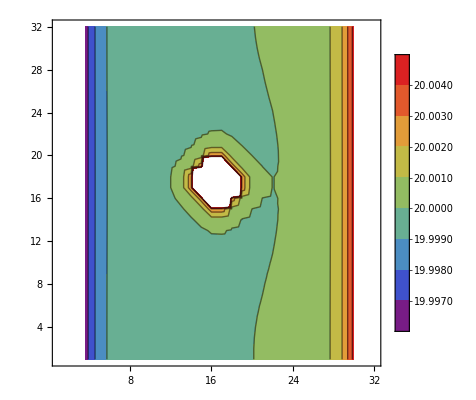

```mathematica
ListContourPlot[ChargeXYPlot,PlotRange->{{1,Lx},{1,Ly}},PlotRange->All,ColorFunction->"Rainbow",PlotLegends->Automatic]
```

```mathematica
ListPlot3D[ChargeXYPlot,PlotRange->{{1,Lx},{1,Ly}},PlotRange->All,ColorFunction->"Rainbow",PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
(** to measure in the unit of e/π, we multiply with π **)
```

```mathematica
(** This is the total charge, so this is actually Q(phi/phi0), not deltaQ(phi/phi0) **)
```

```mathematica
deltaQ = π * Sum[(ChargeXY[[x,y]][[3]])/Lz,{x,midPtX-1,midPtX+2},{y,1,Ly}]
```

402.281

```mathematica
(** First term of dataQ is phi/phi0, and the second term is Q (not deltaQ) at that value of phi/phi0 **)
```

```mathematica
dataQ = {{0,N[128*π]},{0.02,402.1553108919317},{0.04,402.18674743548047 },{0.06,402.21815436089634},{0.08,402.2495165009432},{0.1,402.28081829277346}}
```

{{0,402.124},{0.02,402.155},{0.04,402.187},{0.06,402.218},{0.08,402.25},{0.1,402.281}}

```mathematica
Dimensions[dataQ][[1]]
```

6

```mathematica
(** Here we do the subtraction at the zero magnetic field value, so this is really delta(Q) at phi/phi0 **)
```

```mathematica
dataDeltaQ = Table[{dataQ [[i]][[1]],dataQ [[i]][[2]] - dataQ [[1]][[2]]},{i,1,Dimensions[dataQ][[1]]}]
```

{{0,0.},{0.02,0.0314512},{0.04,0.0628878},{0.06,0.0942947},{0.08,0.125657},{0.1,0.156959}}

```mathematica
fittedslope = D[Fit[dataDeltaQ,{x},x],x]
```

1.57048

```mathematica
N[fittedslope/(π/2)]
```

0.999801

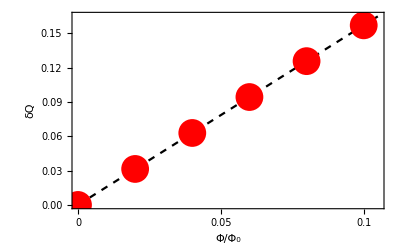

```mathematica
Show[Plot[fittedslope x,{x,0,0.11},PlotStyle->{Dashed,Black}],ListPlot[dataDeltaQ,PlotStyle->{PointSize[0.05], Red}],Frame->True,BaseStyle->18,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},PlotRange->{{0,0.105},{0,0.165}},
RotateLabel->False,FrameTicks->{{0,0.05,0.1},Automatic,{},{}},
FrameLabel-> {"Φ/Φ_0","δQ"}
]
```

```mathematica
(** magnetic field 0.1 -> 64.04897097607557 **)
```

```mathematica
(** magnetic field 0.3 -> delta Q 64.14492972147679 **)
```

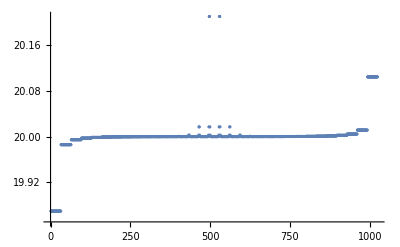

```mathematica
ListPlot[Transpose@{Table[i,{i,1,Lx*Ly}],ChargeXYPlotData},PlotRange->All]
```

```mathematica
Speak["Calculation over"]
```